## Preamble

This section contains the program’s pseudocode and a few definitions that should only need to be executed once (as long as the parameters are not changed).

## Pseudocode

Define the road network.

The network consists of a square grid of stops, with routes running N/S and E/W to define the grid (plus a dummy turnaround loop on each end). Between each pair of grid intersections we can also place stops.

Each stop is a node, whose coordinates we store.

We define arcs for each line, with slightly randomized travel times that depend on distance plus a constant boarding time.

Stops that are close enough to each other (taxicab distance) are connected by walking arcs.

Define population centers and facilities.

Population centers are placed randomly but somewhat evenly spaced on the grid.

Facilities are placed uniformly at random on the grid.

Population centers also receive a random population.

Additional walking arcs are added to connect the new nodes to the network.

Define OD and fleet sizes.

For each stop, decide the travel demand to all other stops according to a gamma distribution based on Euclidean distance.

The total outgoing travel demand for a stop should also depend on its population. For each stop, determine the nearest population center, and equally distribute the center’s population to all of its associated stops.

There should also be an overall scaling factor to adjust the daily traffic as a fraction of the overall population (my Chicago data shows that the number of daily boardings is approximately 2/3 of the total population, but if we are modeling a smaller time period that fraction should be much smaller).

The fleet sizes of each route should be proportional to the number of people using them, which can be quickly modeled by assuming that all of the travel demand travels along its shortest path.

Evaluate the objective function’s shape.

Pick several pairs of lines at random. For each pair, vary both of the fleet sizes within a range and calculate the objective value for each.

Use these results to generate a table of objective values, displayed as an array plot, in order to show how rough the objective looks.

## Parameters

The parameters defined below can be changed to generate different types of example network. Everything below this point should also be re-executed when the parameters are updated.

```mathematica
hlines=6;(* number of grid lines running horizontally *)
vlines=8;(* number of grid lines running vertically *)
hgap=0.2;(* distance between horizontal lines (mi) *)
vgap=0.2;(* distance between vertical lines (mi) *)
jiggle=0.002;(* random displacement for each grid node (mi) *)
horizon=60;(* total time horizon (min) *)
minbetween=0;(* minimum number of nodes to place between grid intersections *)
maxbetween=2;(* maximum number of nodes to place between grid intersections *)
wspeed=0.0455;(* pedestrian walking speed (mi/min) *)
minbspeed=0.3;(* minimum bus speed (mi/min) *)
maxbspeed=0.5;(* maximum bus speed (mi/min) *)
minbstop=0.5;(* minimum bus stop time (min) *)
maxbstop=0.75;(* maximum bus stop time (min) *)
minbturnaround=5;(* minimum bus turnaround time (min) *)
maxbturnaround=30;(* maximum bus turnaround time (min) *)
facilities=10;(* number of facilities *)
populations=20;(* number of population centers *)
popspace=0.2;(* minimum required spacing between population centers (mi) *)
minpop=1000;(* minimum population of a population center *)
maxpop=2000;(* maximum population of a population center *)
wradius=0.12;(* distance cutoff for core walking arcs (mi, measured as taxicab distance) *)
wradius2=0.25;(* distance cutoff for auxiliary walking arcs (mi, measured as taxicab distance) *)
wneighbors=4;(* maximum number of walking neighbors to allow *)
tripmean=1;(* mean passenger trip length (min) *)
tripsd=0.5;(* mean passenger trip std dev (min) *)
```

## Functions

The following functions should only need to be defined when the above parameters are changed.

```mathematica
gamma[x_]:=x^((tripmean^2-tripsd^2)/tripsd^2)E^(-(tripmean/tripsd^2)x);(* gamma distribution of trip length probabilities *)
```

## Execution

The contents of the following sections may need to be repeatedly re-executed to generate satisfactory example networks. They should always be executed in order from top to bottom.

## Network Construction

This section builds the underlying network of stops and other locations, along with the line arcs and walking arcs to connect them. A map of the network is shown once this process is complete.

```mathematica
(* Initialize data structures *)
ncoords={};(* list of node coordinates *)
ntype={};(* list of node types (0 for stop, 1 for boarding, 2 for population, 3 for facility) *)
stops={};(* subset of stop node IDs *)
nname={};(* list of node names *)
nline={};(* list of boarding node line IDs *)
nval={};(* list of node values (population or facility weight as applicable) *)
nrows={};(* list of lists of boarding node IDs for each street row *)
ncols={};(* list of lists of boarding node IDs for each street column *)
arcs={};(* list of arcs, in i->j format *)
atype={};(* list of arc types (0 for line, 1 for boarding, 2 for alighting, 3 for core walking, 4 for accessibility walking) *)
acost={};(* list of arc times *)
alines={};(* list of lists of line arc IDs for each transit line *)

Print["Dimensions (mi): "<>ToString[(hlines-1) hgap]<>" × "<>ToString[(vlines-1) vgap]](* display dimensions of network *)
Print["Lines: "<>ToString[hlines+vlines]](* display number of routes *)

(* Generate grid intersection stops *)
ncoords=Flatten[Table[{vgap j,hgap i},{i,0,hlines-1},{j,0,vlines-1}],1]+RandomReal[{-jiggle,jiggle},{hlines vlines,2}];

(* Insert additional stops between grid intersections and build up the row/column lists *)
Module[{col,row,inc},
Do[
(* process each column from bottom to top *)
col={};(* node IDs in current column *)
Do[
col=Append[col,(i-1)+vlines (j-1)+1];(* current node ID *)
btw=RandomInteger[{minbetween,maxbetween}];(* number of stops to insert *)
inc=N[hgap/(btw+1)];(* distance north of current stop *)
Do[
(* insert stops between consecutive intersections *)
ncoords=Append[ncoords,ncoords[[(col[[-1]])]]+{0,inc}+RandomReal[{-jiggle,jiggle},2]];(* new stop coordinate *)
col=Append[col,Length[ncoords]](* add new entry to column list *),
{k,1,btw}],
{j,1,hlines-1}];
(* topmost stop requires separate processing *)
col=Append[col,(i-1)+vlines (hlines-1)+1];(* top stop *)
ncols=Append[ncols,col](* add all stops in column to main column list *),
{i,1,vlines}];
Do[
(* process each row from left to right *)
row={};(* node IDs in current row *)
Do[
row=Append[row,vlines(i-1)+(j-1)+1];(* current node ID *)
btw=RandomInteger[{minbetween,maxbetween}];(* number of stops to insert *)
inc=N[vgap/(btw+1)];(* distance east of current stop *)
Do[
(* insert stops between consecutive intersections *)
ncoords=Append[ncoords,ncoords[[(row[[-1]])]]+{inc,0}];(* new stop coordinate *)
row=Append[row,Length[ncoords]](* add new entry to row list *),
{k,1,btw}],
{j,1,vlines-1}];
(* rightmost stop requires separate processing *)
row=Append[row,vlines i];(* right stop *)
nrows=Append[nrows,row](* add all stops in row to main row list *),
{i,1,hlines}];

(* generate node attributes *)
ntype=ConstantArray[0,Length[ncoords]];(* stops are type 0 *)
nline=ConstantArray[-1,Length[ncoords]];(* stops have no associated lines *)
nname=Table["Stop"<>ToString[i],{i,1,Length[ncoords]}];(* stop nodes are named according to their node IDs *)
stops=Table[i,{i,1,Length[ncoords]}];(* all nodes so far are stops *)
Print["Stops: "<>ToString[Length[ncoords]]];(* print number of stops *)
];

(* Define boarding nodes and associated boarding/alighting arcs for each column and row *)
Module[{old,new},
Do[
(* process each column from bottom to top *)
Do[
old=ncols[[i,j]];(* node ID of current stop *)
new=Length[ncoords]+1;(* node ID of new boarding node *)
ncoords=Append[ncoords,ncoords[[old]]];(* boarding node gets same coordinates as stop *)
nname=Append[nname,nname[[old]]<>"_Route"<>ToString[i]];(* append line ID to boarding node name *)
nline=Append[nline,i];(* boarding node associated with current line *)
ntype=Append[ntype,1];(* boarding nodes are type 1 *)
arcs=Join[arcs,{old->new,new->old}];(* add boarding and alighting arcs *)
acost=Join[acost,{0,0}];(* boarding and alighting base times both 0 *)
atype=Join[atype,{1,2}];(* boarding type 1, alighting type 2 *)
ncols[[i,j]]=Length[ncoords];(* replace line node ID with the new node for later use *),
{j,1,Length[(ncols[[i]])]}],
{i,1,vlines}];
Do[
(* process each row from left to right *)
Do[
old=nrows[[i,j]];(* node ID of current stop *)
new=Length[ncoords]+1;(* node ID of new boarding node *)
ncoords=Append[ncoords,ncoords[[old]]];(* boarding node gets same coordinates as stop *)
nname=Append[nname,nname[[old]]<>"_Route"<>ToString[i]];(* append line ID to boarding node name *)
nline=Append[nline,vlines+i];(* boarding node associated with current line *)
ntype=Append[ntype,1];(* boarding nodes are type 1 *)
arcs=Join[arcs,{old->new,new->old}];(* add boarding and alighting arcs *)
acost=Join[acost,{0,0}];(* boarding and alighting base times both 0 *)
atype=Join[atype,{1,2}];(* boarding type 1, alighting type 2 *)
nrows[[i,j]]=Length[ncoords];(* replace line node ID with the new node for later use *),
{j,1,Length[(nrows[[i]])]}],
{i,1,hlines}];

nval=ConstantArray[-1,Length[ncoords]];(* stop and boarding nodes have no values *)
];

(* Define line arcs for each column and row *)
Module[{head,tail,line,d,t},
Do[
(* process each column and generate arcs between each consecutive pair of stops *)
line={};(* current transit line's arcs *)
Do[
tail=ncols[[i,j]];(* tail stop ID *)
head=ncols[[i,j+1]];(* head stop ID *)
d=EuclideanDistance[ncoords[[tail]],ncoords[[head]]];(* link distance *)
t=RandomReal[{minbstop,maxbstop}]+d/RandomReal[{minbspeed,maxbspeed}];(* link time *)
acost=Append[acost,t];
atype=Append[atype,0];
line=Append[line,tail->head];(* append arc to line list *)
(* also generate revese arc *)
t=RandomReal[{minbstop,maxbstop}]+d/RandomReal[{minbspeed,maxbspeed}];
acost=Append[acost,t];
atype=Append[atype,0];
line=Append[line,head->tail],
{j,1,Length[ncols[[i]]]-1}];
(* add turnaround loops to endpoints *)
line=Append[line,ncols[[i,1]]->ncols[[i,1]]];
acost=Append[acost,RandomReal[{minbturnaround,maxbturnaround}]];
line=Append[line,ncols[[i,-1]]->ncols[[i,-1]]];
acost=Append[acost,RandomReal[{minbturnaround,maxbturnaround}]];
atype=Join[atype,{0,0}];
arcs=Join[arcs,line];(* add arcs to main arc list *)
alines=Append[alines,line](* add line arcs to line arc list *),
{i,1,Length[ncols]}];
Do[
(* process each row and generate arcs between each consecutive pair of stops *)
line={};(* current transit line's arcs *)
Do[
tail=nrows[[i,j]];(* tail stop ID *)
head=nrows[[i,j+1]];(* head stop ID *)
d=EuclideanDistance[ncoords[[tail]],ncoords[[head]]];(* link distance *)
t=RandomReal[{minbstop,maxbstop}]+d/RandomReal[{minbspeed,maxbspeed}];(* link time *)
acost=Append[acost,t];
atype=Append[atype,0];
line=Append[line,tail->head];(* append arc to line list *)
(* also generate revese arc *)
t=RandomReal[{minbstop,maxbstop}]+d/RandomReal[{minbspeed,maxbspeed}];
acost=Append[acost,t];
atype=Append[atype,0];
line=Append[line,head->tail],
{j,1,Length[nrows[[i]]]-1}];
(* add turnaround loops to endpoints *)
line=Append[line,nrows[[i,1]]->nrows[[i,1]]];
acost=Append[acost,RandomReal[{minbturnaround,maxbturnaround}]];
line=Append[line,nrows[[i,-1]]->nrows[[i,-1]]];
acost=Append[acost,RandomReal[{minbturnaround,maxbturnaround}]];
atype=Join[atype,{0,0}];
arcs=Join[arcs,line];(* add arcs to main arc list *)
alines=Append[alines,line](* add line arcs to line arc list *),
{i,1,Length[nrows]}];
];

(* Generate core walking arcs *)
Module[{d,t,a,b},
Do[
Do[
(* process each unique pair of stop nodes *)
a=stops[[i]];
b=stops[[j]];
d=ManhattanDistance[ncoords[[a]],ncoords[[b]]];(* pairwise distance *)
t=N[d/wspeed];(* walking time *)
If[d≤wradius,
(* connect nearby pairs of arcs with walking arcs *)
(************************************************************)
(* add quadrangle check if there are too many walking arcs *)
(************************************************************)
arcs=Join[arcs,{a->b,b->a}];
atype=Join[atype,{3,3}];
acost=Join[acost,{t,t}];
],
{j,1,i-1}],
{i,1,Length[stops]}];
];

Print["Nodes: "<>ToString[Length[ncoords]]];
Print["Arcs: "<>ToString[Length[arcs]]];

(* Display map for review *)
Module[{as={}},
Do[
(* pick subset of arcs that are not boarding or alighting, since otherwise Mathematica will have trouble drawing things *)
If[atype[[i]]≠1&&atype[[i]]≠2,
as=Append[as,arcs[[i]]];
],
{i,1,Length[arcs]}];
Graph[Table[i,{i,1,Length[ncoords]}],as,VertexCoordinates->ncoords]
]
```

Dimensions (mi): 1. × 1.4

Lines: 14

Stops: 128

Nodes: 304

Arcs: 968

-Graphics-

## Population and Facility Generation

This section adds population center and facility nodes to the base network defined above. The updated map is shown for review.

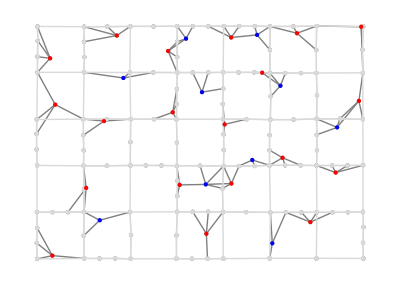

```mathematica
(* Initialize data structures *)
pcoords={};(* population center coordinates *)
pname={};(* population center names *)
pval={};(* population center populations *)
pid={};(* population center node IDs *)
fcoords={};(* facility coordinates *)
fname={};(* facility names *)
fval={};(* facility quality metrics *)
fid={};(* facility node IDs *)
anew={};(* population and facility walking arcs *)
anewcost={};(* costs of new walking arcs *)

(* Generate population centers *)
Module[{p=0,c,accept,fails=0,cutoff=500},
pid=Table[Length[ncoords]+i,{i,1,populations}];(* generate node IDs *)
While[p<populations,
(* try placing population centers, but repeat if it's too close to an existing center *)
accept=True;(* whether to accept candidate *)
c={RandomReal[(vlines-1)vgap],RandomReal[(hlines-1)hgap]};(* candidate *)
If[fails≤cutoff,
(* only bother with the closeness check if we haven't seen too many failures so far *)
Do[
(* check distance to all accepted population centers *)
If[EuclideanDistance[c,pcoords[[i]]]<popspace,
accept=False;(* reject candidate for being too close *)
fails+=1;(* increment fail count *)
Break[];(* break if too close *)
],
{i,1,Length[pcoords]}];
];
If[accept==True,
(* add accepted candidate to list *)
pcoords=Append[pcoords,c];
p+=1;
];
];

(*pcoords=Transpose[{RandomReal[(vlines-1) vgap,populations],RandomReal[(hlines-1) hgap,populations]}];*)(* randomized coordinates *)
pname=Join[nname,Table["Pop"<>ToString[i],{i,1,populations}]];(* names of population centers *)
pval=RandomInteger[{minpop,maxpop},populations];(* randomize populations *)
];

(* Generate facilities *)
Module[{},
fid=Table[Length[ncoords]+populations+i,{i,1,facilities}];(* generate node IDs *)
fcoords=Transpose[{RandomReal[(vlines-1) vgap,facilities],RandomReal[(hlines-1) hgap,facilities]}];(* randomized coordinates *)
fname=Join[nname,Table["Fac"<>ToString[i],{i,1,facilities}]];(* names of facilities *)
fval=ConstantArray[1,facilities];(* constant value *)
];

(* Generate additional walking arcs *)
Module[{nbhd,a,b,blist,temp,d,t},
Do[
(* process each population center and attach it to its nearest few nodes *)
a=pid[[i]];(* current node *)
nbhd=Nearest[Join[ncoords[[stops]],pcoords[[1;;i-1]],pcoords[[i+1;;]],fcoords],pcoords[[i]],{wneighbors,wradius2}];(* set of nearby stop coordinates *)
If[Length[nbhd]==0,
(* report isolated nodes *)
Print["Stranded node."];
];
(* generate walking arcs between the current node and its chosen neighbors *)
Do[
(* find IDs corresponding to coordinate *)
d=ManhattanDistance[pcoords[[i]],nbhd[[j]]];
t=N[d/wspeed];
blist={};(* list of node IDs that match the current coordinate *)
temp=Flatten[Position[ncoords[[stops]],nbhd[[j]]]];
If[Length[temp]>0,
blist=temp;
];
temp=Flatten[Position[pcoords,nbhd[[j]]]];
If[Length[temp]>0,
blist=Join[blist,temp+Length[ncoords]];
];
temp=Flatten[Position[fcoords,nbhd[[j]]]];
If[Length[temp]>0,
blist=Join[blist,temp+populations+Length[ncoords]];
];
(* generate walking arcs to all chosen IDs *)
Do[
b=blist[[k]];
anew=Join[anew,{a->b,b->a}];
anewcost=Join[anewcost,{t,t}],
{k,1,Length[blist]}],
{j,1,Length[nbhd]}],
{i,1,Length[pcoords]}];
Do[
(* process each facility and attach it to its nearest few nodes *)
a=fid[[i]];(* current node *)
nbhd=Nearest[Join[ncoords[[stops]],fcoords[[1;;i]],fcoords[[i+1;;]]],fcoords[[i]],{wneighbors,wradius2}];(* set of nearby stop coordinates *)
If[Length[nbhd]==0,
(* report isolated nodes *)
Print["Stranded node."];
];
(* generate walking arcs between the current node and its chosen neighbors *)
Do[
(* find IDs corresponding to coordinate *)
d=ManhattanDistance[fcoords[[i]],nbhd[[j]]];
t=N[d/wspeed];
blist={};(* list of node IDs that match the current coordinate *)
temp=Flatten[Position[ncoords[[stops]],nbhd[[j]]]];
If[Length[temp]>0,
blist=temp;
];
temp=Flatten[Position[fcoords,nbhd[[j]]]];
If[Length[temp]>0,
blist=Join[blist,temp+populations+Length[ncoords]];
];
(* generate walking arcs to all chosen IDs *)
Do[
b=blist[[k]];
anew=Join[anew,{a->b,b->a}];
anewcost=Join[anewcost,{t,t}],
{k,1,Length[blist]}],
{j,1,Length[nbhd]}],
{i,1,Length[fcoords]}];
];

(* Display map for review *)
Module[{as={}},
Do[
(* pick subset of arcs that are not boarding or alighting, since otherwise Mathematica will have trouble drawing things *)
If[atype[[i]]≠1&&atype[[i]]≠2,
as=Append[as,arcs[[i]]];
],
{i,1,Length[arcs]}];
Show[GraphPlot[Graph[Table[i,{i,1,Length[ncoords]+Length[pcoords]+Length[fcoords]}],anew,VertexCoordinates->Join[ncoords,pcoords,fcoords]],PlotStyle->{Gray},DirectedEdges->False],GraphPlot[Graph[Table[i,{i,1,Length[ncoords]}],as,VertexCoordinates->ncoords],PlotStyle->{LightGray},DirectedEdges->False],GraphPlot[Graph[Table[i,{i,1,populations}],{},VertexCoordinates->pcoords],PlotStyle->{Red,PointSize[Large]}],GraphPlot[Graph[Table[i,{i,1,facilities}],{},VertexCoordinates->fcoords],PlotStyle->{Blue,PointSize[Medium]}]]
]
```

## Travel Demand and Fleet Size

The following section generates travel demand (based on population and an assumed gamma distribution of trip lengths) and uses this to assign initial fleet sizes.

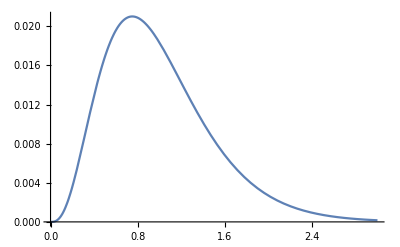

```mathematica
(* Initialize data structures *)
od=ConstantArray[0,{Length[stops],Length[stops]}];(* full OD matrix *)

(* OD Matrix:
-Generate a list of stops associated with each popluation center.
-Find the fraction of transit-using population of each center, and use that along with the stop lists to (approximately) evenly distribute the population center's population to each stop as origin traffic.
-Use Manhattan distance to approximately calculate travel times from one stop to every other stop.
-Use these times along with the gamma function to generate a trip probability weight for that OD pair.
-Use the weight to distribute the origin traffic to each of the destinations for the full OD demand.
-Add some random noise, and zero out travel demands that are too small. *)

(* Fleet Size:
-For each OD pair (with nonzero demand), find the shortest path on the graph and take note of which arcs are used. Maintain for each arc a tally of the total traffic through it. Alternatively, for simplicity, maintain a tally for the lines instead of individual arcs.
-Apply the vehicles proportionally to the lines according to their travel volume, plus some constant, and then add some random noise.
-Calculate a load factor for reference, since ideally we would like for the total travel demand to be 1-1.5x the total vehicle capacity. *)

(* Display results *)
Plot[gamma[x],{x,0,3tripmean}]
```

## Objective Topology

The section below randomly selects pairs of transit lines, adjusts both of their fleet sizes within ranges around their initial values, and displays tables of the objective value with respect to the two decision variables. Ideally we would like to see a rough response.

```mathematica
(* CAN WAIT UNTIL AFTER GETTING SINGLE SOLVER DONE:
Then move into the objective calculation module.
Write a simple program to calculate pairwise network distances based on the weighted graph.
Write a program to evaluate the facility metric of any facility, and then the population metric of any population, and finally the overall k-sum objective.
All of the above depends on the waiting times that come from the initial fleet sizes, but we also need to be able to look at waiting times for other fleet sizes. *)
```

## File Export

If all of the above tests are to the user’s liking, the following section can be used to export the full set of example network files, plus an additional node coordinate file for use in drawing the network.

```mathematica
(* WIP *)
```